```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-((2857-(5033/9)Nf+(325/27) Nf^2)/128); (*for Nc=3 only*)
β3[Nf_]=((-1)/256)((149753/6+3564 Zeta[3])-(1078361/162+(6508/27) Zeta[3])Nf+(50065/162+(6472/81)Zeta[3])Nf^2+(1093/729) Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=(1/16)(202/3-(20/9)Nf);(*for Nc=3 only*)
γ2[Nf_]=(1/64)(1249+(-(2216/27)-(160/3) Zeta[3])Nf-(140/81) Nf^2);(*for Nc=3 only*)
γ3[Nf_]=(1/256)(4603055/162+(135680/27) Zeta[3]-8800Zeta[5]+(-(91723/27)-(34192/9) Zeta[3]+880 Zeta[4]+(18400/9)Zeta[5])Nf+(5242/243+(800/9) Zeta[3]-(160/3)Zeta[4])Nf^2+(-(332/243)+(64/27) Zeta[3])Nf^3);

b0[Nf_]=-((8β0[Nf])/(2(4π)^2));
b1[Nf_]=-((32 β1[Nf])/(2(4π)^2));

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=(-1)/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-( β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+(1/(β0[Nf]^7 t^4))( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Generate Spectral Functions

```mathematica
R=20000;
Mc=1.4689725245671532;
Mb=4.882;
kfinal={0.6802525363662164,-0.31465604392609736};(*100k run*)
kfinalu={0.9017845365143496,-0.3669424499609976};
kfinall={0.4587205362180833,-0.26236963789119705};
αcont={0.5146004500017507,0.002579680095957094};(*10k run*)
σcont={0.16904257426266697,0.0009046347484072015};
ccont={-0.15782092474161866,0.0024785523617348124};
rsb=1.542442506842263/0.197327;
conv=0.197327;
```

### Define required functions

```mathematica
ImVc[r_,mD_,α_,T_]:=T α NIntegrate[(2 z (1-Sinc[mD r z]))/((z^2+1)^2),{z,0,∞},MaxRecursion->20];
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
ImVsb[r_,mD_,α_,σ_,T_]:=Piecewise[{{T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4],r<rsb},{T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 rsb^2)/4])+1/4 mD √π (rsb)^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 (rsb)^2)/4],r≥rsb}}];
ReV[r_,m_,α_,σ_,c_]:=c-α m-α Exp[-m r]/r+(2 σ)/m-(ⅇ^(-m r) (2+m r) σ)/m;
ReVsb[r_,mD_,α_,σ_,c_]:=Piecewise[{{c-α mD-α Exp[-mD r]/r+(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD,r<rsb},{c-α mD-α Exp[-mD rsb]/rsb+(2 σ)/mD-(ⅇ^(-mD rsb) (2+mD rsb) σ)/mD,r≥rsb}}];
ReVm0[r_,α_,σ_,c_]:=-α/r+σ r+c
```

```mathematica
mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
mDcalmu[T_,μ_,c_,d_]:=Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ];
```

### Modules

```mathematica
ParallelSow[expr_]:=Sow[expr];
SetSharedFunction[ParallelSow];
```

```mathematica
δ=1/100; 
dω=0.0002;
```

#### Charmonium s - wave

```mathematica
swaveccspectra[n_,Tmuscan_]:=Block[{s=Tmuscan[[n,1]],T=Tmuscan[[n,2]],μ=Tmuscan[[n,3]],mD=mDcalmu[Tmuscan[[n,2]],Tmuscan[[n,3]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,26,1500,1}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(( 6 Nc M^2 α)/(4π))Im[1/(gr0[x])^2(*+(36/(gr1[x])^2)*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectraldata/Snnscan/cc/swccs"<>ToString[s]<>"spectra.dat",Sort[ccss]];
];
```

```mathematica
swaveccuspectra[n_,Tmuscan_]:=Block[{s=Tmuscan[[n,1]],T=Tmuscan[[n,2]],μ=Tmuscan[[n,3]],mD=mDcalmu[Tmuscan[[n,2]],Tmuscan[[n,3]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,26,1500,1}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(( 6 Nc M^2 α)/(4π))Im[1/(gr0[x])^2(*+(36/(gr1[x])^2)*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectraldata/Snnscan/cc/swccs"<>ToString[s]<>"uspectra.dat",Sort[ccss]];
];
```

```mathematica
swavecclspectra[n_,Tmuscan_]:=Block[{s=Tmuscan[[n,1]],T=Tmuscan[[n,2]],μ=Tmuscan[[n,3]],mD=mDcalmu[Tmuscan[[n,2]],Tmuscan[[n,3]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,26,1500,1}],ParallelTable[{r,ImVsb[r,mD,α,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(( 6 Nc M^2 α)/(4π))Im[1/(gr0[x])^2(*+(36/(gr1[x])^2)*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectraldata/Snnscan/cc/swccs"<>ToString[s]<>"lspectra.dat",Sort[ccss]];
];
```

#### Charmonium s-wave without string breaking

```mathematica
ImV[r_,mD_,α_,σ_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

```mathematica
ImVc[1000000,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],αcont[[1]],0.155]
```

0.0797631

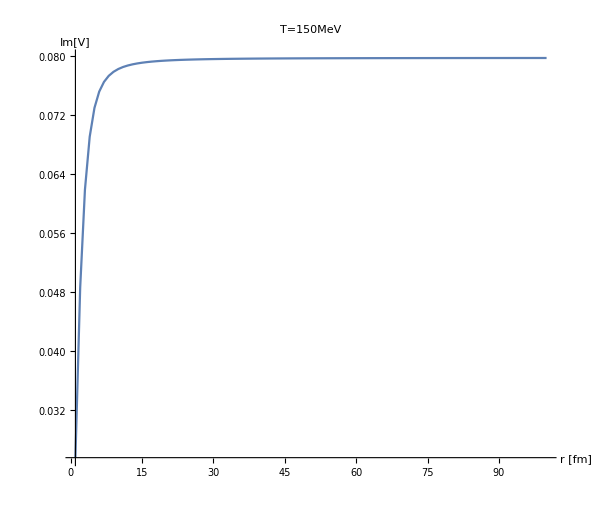

```mathematica
Block[{mD=mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]]},Show[DiscretePlot[ImVc[r/0.197,mD,αcont[[1]],0.155],{r,1,100,1},Joined->True,Filling->None,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotRange->All,AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=150MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]]]
```

```mathematica
Series[1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4],{r,∞,10}]//FullSimplify
```

ⅇ^(-ⅈ √(-mD^2) r) ((mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π+ⅈ Log[-mD^2]-ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]))/((mD^2)^(3/2))+O[1/r]^7)+ⅇ^(ⅈ √(-mD^2) r) ((mD T σ (ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π-ⅈ Log[-mD^2]+ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(√(mD^2) T σ (ⅈ π+Log[-mD^2]-Log[mD^2]))/mD^3+O[1/r]^7)+((2 √(mD^2) T σ (-2+2 EulerGamma+Log[mD^2]-2 Log[1/r]))/mD^3-(16 (√(mD^2) T σ))/(mD^5 r^2)-(216 (√(mD^2) T σ))/(mD^7 r^4)-(7680 (√(mD^2) T σ))/(mD^9 r^6)+O[1/r]^8)

```mathematica
ImVsS[r_,mD_,σ_,T_]:=(2 √(mD^2) T σ (-2+2 EulerGamma+Log[mD^2]-2 Log[1/r]))/mD^3-(16 (√(mD^2) T σ))/(mD^5 r^2)-(216 (√(mD^2) T σ))/(mD^7 r^4)-(7680 (√(mD^2) T σ))/(mD^9 r^6)ⅇ^(ⅈ √(-mD^2) r)((mD T σ (ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π-ⅈ Log[-mD^2]+ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(√(mD^2) T σ (ⅈ π+Log[-mD^2]-Log[mD^2]))/mD^3)+ⅇ^(-ⅈ √(-mD^2) r)((mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π+ⅈ Log[-mD^2]-ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]))/((mD^2)^(3/2)));
```

```mathematica
ImVsS[169,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

7.65902-2.14767×10^-18 ⅈ

```mathematica
ImVs[140,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

7.64838

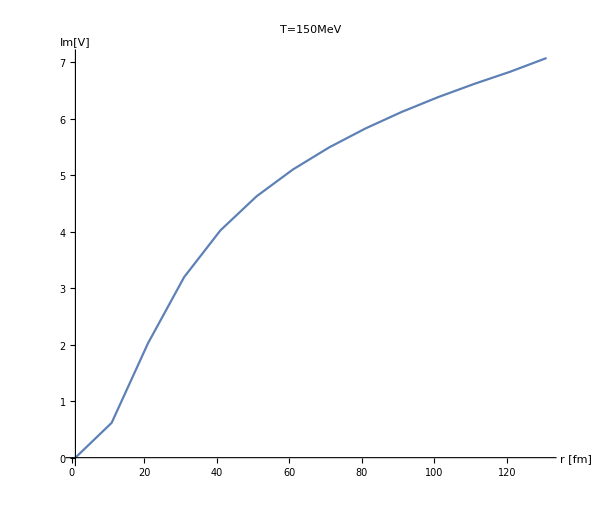

```mathematica
Block[{mD=mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]]},Show[DiscretePlot[ImVs[r,mD,σcont[[1]],0.155],{r,1,140,10},Joined->True,Filling->None,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotRange->All,AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=150MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]]]
```

```mathematica
ImVs[20000,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

4.5458052209354×10^1789

```mathematica
ImVsS[20000,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

19.3543+0. ⅈ

```mathematica
swaveccspectrawsb[n_,Tmuscan_]:=Block[{s=Tmuscan[[n,1]],T=Tmuscan[[n,2]],μ=Tmuscan[[n,3]],mD=mDcalmu[Tmuscan[[n,2]],Tmuscan[[n,3]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V},

rev=Interpolation[Join[ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,26,140,1}],ParallelTable[{r,ImVc[r,mD,α,T]+ImVsS[r+18,mD,σ,T]},{r,141,1500,1}],ParallelTable[{r,ImVc[r+18,mD,α,T]+ImVsS[r,mD,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectraldata/Snnscan/ccwsb/swccT"<>ToString[s]<>"spectra.dat",Sort[ccss]];
];
```

```mathematica
swavecclspectrawsb[n_,Tmuscan_]:=Block[{s=Tmuscan[[n,1]],T=Tmuscan[[n,2]],μ=Tmuscan[[n,3]],mD=mDcalmu[Tmuscan[[n,2]],Tmuscan[[n,3]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V},

rev=Interpolation[Join[ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,26,140,1}],ParallelTable[{r,ImVc[r,mD,α,T]+ImVsS[r+18,mD,σ,T]},{r,141,1500,1}],ParallelTable[{r,ImVc[r+18,mD,α,T]+ImVsS[r,mD,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectraldata/Snnscan/ccwsb/swccT"<>ToString[s]<>"lspectra.dat",Sort[ccss]];
];
```

```mathematica
swaveccuspectrawsb[n_,Tmuscan_]:=Block[{s=Tmuscan[[n,1]],T=Tmuscan[[n,2]],μ=Tmuscan[[n,3]],mD=mDcalmu[Tmuscan[[n,2]],Tmuscan[[n,3]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V},

rev=Interpolation[Join[ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReV[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,26,140,1}],ParallelTable[{r,ImVc[r,mD,α,T]+ImVsS[r+18,mD,σ,T]},{r,141,1500,1}],ParallelTable[{r,ImVc[r+18,mD,α,T]+ImVsS[r,mD,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectraldata/Snnscan/ccwsb/swccT"<>ToString[s]<>"spectrau.dat",Sort[ccss]];
];
```

### Statistical model √s_NN

```mathematica
(* s here is √Subscript[s, NN]in GeV*)
Tlim=0.155;
T[s_]:=Tlim (1/(1+Exp[1.72-Log[s/0.45]]));
μ[s_]:=(1303 10^-3)/(1+0.286 s);
```

```mathematica
Tmuscan=Join[Table[{i,T[i],μ[i]},{i,8,195,10}],Table[{i,T[i],μ[i]},{i,200,1000,100}],Table[{i,T[i],μ[i]},{i,2000,10000,1000}]]
```

{{8,0.117949,0.39629},{18,0.136011,0.211939},{28,0.142234,0.144649},{38,0.145385,0.109791},{48,0.147289,0.0884709},{58,0.148563,0.0740846},{68,0.149476,0.0637226},{78,0.150162,0.0559036},{88,0.150697,0.0497936},{98,0.151125,0.0448877},{108,0.151475,0.0408618},{118,0.151768,0.0374986},{128,0.152015,0.0346469},{138,0.152228,0.0321983},{148,0.152412,0.0300729},{158,0.152573,0.0282108},{168,0.152716,0.0265658},{178,0.152842,0.0251021},{188,0.152955,0.0237913},{200,0.153077,0.0223883},{300,0.153712,0.0150115},{400,0.154032,0.0112912},{500,0.154225,0.00904861},{600,0.154354,0.00754925},{700,0.154446,0.00647614},{800,0.154515,0.00567015},{900,0.154568,0.00504257},{1000,0.154611,0.00454007},{2000,0.154805,0.002274},{3000,0.15487,0.00151688},{4000,0.154903,0.00113799},{5000,0.154922,0.000910552},{6000,0.154935,0.000758882},{7000,0.154944,0.000650524},{8000,0.154951,0.000569244},{9000,0.154957,0.000506019},{10000,0.154961,0.000455435}}

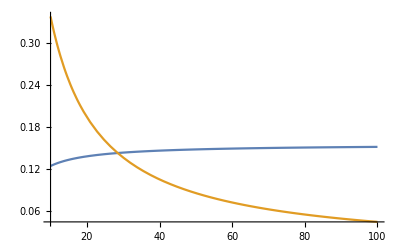

```mathematica
Plot[{T[s],μ[s]},{s,10,100}]
```

### Run modules

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
Tmuscan[[-2;;]]
```

{{9000,0.154957,0.000506019},{10000,0.154961,0.000455435}}

```mathematica
Do[swaveccspectrawsb[i,Tmuscan[[-7;;]]],{i,Length[Tmuscan[[-7;;]]]}]//AbsoluteTiming
```

```mathematica
Do[swavecclspectrawsb[i,Tmuscan[[-20;;]]],{i,Length[Tmuscan[[-20;;]]]}]//AbsoluteTiming
```

```mathematica
Do[swaveccuspectrawsb[i,Tmuscan[[-2;;]]],{i,Length[Tmuscan[[-2;;]]]}]//AbsoluteTiming
```

{9912.77,Null}

## Continuum Energies

```mathematica
2Mc+Table[ReVsb[100000,mDcalmu[Tmuscan[[i,2]],Tmuscan[[i,3]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tmuscan]}]
```

{3.68991,3.77307,3.78196,3.77609,3.76859,3.76185,3.75619,3.75148,3.74755,3.74423,3.74142,3.73899,3.73689,3.73505,3.73343,3.73199,3.7307,3.72955,3.7285,3.72737,3.72129,3.71813,3.7162,3.71489,3.71395,3.71324,3.71269,3.71224,3.71022,3.70954,3.7092,3.70899,3.70886,3.70876,3.70869,3.70863,3.70858}

```mathematica
2Mc+Table[ReVsb[100000,mDcalmu[Tmuscan[[i,2]],Tmuscan[[i,3]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tmuscan]}]
```

{3.68991,3.77307,3.78196,3.77609,3.76859,3.76185,3.75619,3.75148,3.74755,3.74423,3.74142,3.73899,3.73689,3.73505,3.73343,3.73199,3.7307,3.72955,3.7285,3.72737,3.72129,3.71813,3.7162,3.71489,3.71395,3.71324,3.71269,3.71224,3.71022,3.70954,3.7092,3.70899,3.70886,3.70876,3.70869,3.70863,3.70858}

```mathematica
2Mc+Table[ReVsb[100000,mDcalmu[Tmuscan[[i,2]],Tmuscan[[i,3]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tmuscan]}]
```

{3.5526,3.60634,3.60689,3.59727,3.58772,3.57975,3.57328,3.56801,3.56367,3.56005,3.557,3.55439,3.55213,3.55017,3.54844,3.54692,3.54556,3.54434,3.54324,3.54205,3.5357,3.53242,3.53042,3.52907,3.5281,3.52737,3.5268,3.52634,3.52427,3.52357,3.52323,3.52302,3.52288,3.52278,3.5227,3.52264,3.5226}